## Higher order crap

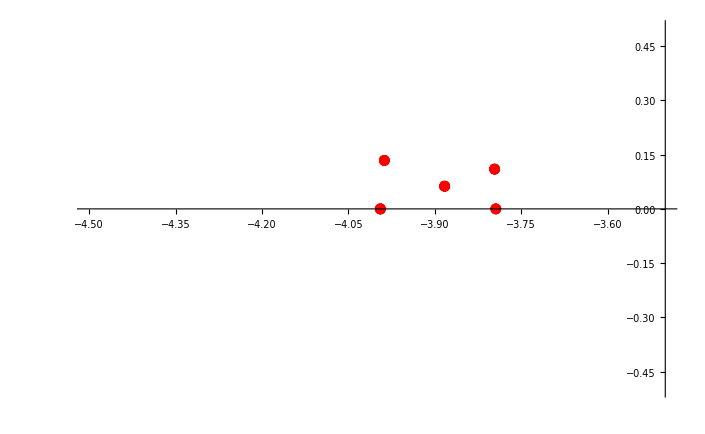
```mathematica
Clear[var];{a1,b1,c1,d1,a2,c2,k12}={4,1.2,var,-1,4.3,-4,var2};
equations={d1 g+2c1 x1+b1 x1^2+a1 x1^3-k12 (-x1+x2),d2 g-k21 (x1-x2)+2c2 x2+b2 x2^2+a2 x2^3};
k21=k12;k31=k13;k41=k14;k32=k23;k42=k24;k43=k34;b2=1;b3=b1;b4=b1;d2=d1;d3=d1;d4=d1;
jacobian=D[equations,{{x1,x2}}];
nullvector=(NullSpace[{{A11,A12},{A12,A12^2/A11}}])/.{A11->D[equations[[1]],x1],A12->D[equations[[1]],x2]};
triplecrossing={x1,x2,x3,x4,x5,x6,g,var,var2}/.NSolve[{equations==0&&Det@jacobian==0&&(equations/.{x1->x3,x2->x4})==0&&(Det[jacobian/.{x1->x3,x2->x4}])==0&&(equations/.{x1->x5,x2->x6})==0&&(Det[jacobian/.{x1->x5,x2->x6}])==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3&&Abs[x5]<3&&Abs[x6]<3&&-4.5<=var<=-3.5&&-.5<=var2<=.5},{x1,x2,x3,x4,x5,x6,g,var,var2},Reals];
twocrossings={x1,x2,x3,x4,x5,x6,x7,x8,g,g2,var,var2}/.NSolve[{equations==0&&Det@jacobian==0&&(equations/.{x1->x3,x2->x4})==0&&(Det[jacobian/.{x1->x3,x2->x4}])==0&&(equations/.{x1->x5,x2->x6,g->g2})==0&&(Det[jacobian/.{x1->x5,x2->x6,g->g2}])==0&&(equations/.{x1->x7,x2->x8,g->g2})==0&&(Det[jacobian/.{x1->x7,x2->x8,g->g2}])==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3&&Abs[x5]<3&&Abs[x6]<3&&Abs[x7]<3&&Abs[x8]<3&&-4.5<=var<=-3.5&&-.5<=var2<=.5},{x1,x2,x3,x4,x5,x6,x7,x8,g,g2,var,var2},Reals];
doublecusppoints={x1,x2,x3,x4,g,g2,var,var2}/.NSolve[{equations==0&&Det@jacobian==0&&nullvector.{D[D[equations[[1]],x1],x1]*nullvector[[1,1]]^2,D[D[equations[[2]],x2],x2]*nullvector[[1,2]]^2}==0&&(equations/.{x1->x3,x2->x4,g->g2})==0&&(Det[jacobian/.{x1->x3,x2->x4,g->g2}])==0&&((nullvector.{D[D[equations[[1]],x1],x1]*nullvector[[1,1]]^2,D[D[equations[[2]],x2],x2]*nullvector[[1,2]]^2})/.{x1->x3,x2->x4,g->g2})==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3&&-4.5<=var<=-3.5&&-.5<=var2<=.5},{x1,x2,x3,x4,g,g2,var,var2},Reals];
cuspcrossing={x1,x2,x3,x4,x5,x6,g,g2,var,var2}/.NSolve[{equations==0&&Det@jacobian==0&&nullvector.{D[D[equations[[1]],x1],x1]*nullvector[[1,1]]^2,D[D[equations[[2]],x2],x2]*nullvector[[1,2]]^2}==0&&(equations/.{x1->x3,x2->x4,g->g2})==0&&(Det[jacobian/.{x1->x3,x2->x4,g->g2}])==0&&(equations/.{x1->x5,x2->x6,g->g2})==0&&(Det[jacobian/.{x1->x5,x2->x6,g->g2}])==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3&&-4.5<=var<=-3.5&&-.5<=var2<=.5},{x1,x2,x3,x4,x5,x6,g,g2,var,var2},Reals];
mainlist=Join[DeleteDuplicates[triplecrossing],DeleteDuplicates[twocrossings],DeleteDuplicates[doublecusppoints],DeleteDuplicates[cuspcrossing]];
eig1=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[1]],x2->#[[2]],g->#[[9]],var->#[[11]],var2->#[[12]]}&/@twocrossings)[[n]]],{n,1,Length@twocrossings}];
eig2=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[3]],x2->#[[4]],g->#[[9]],var->#[[11]],var2->#[[12]]}&/@twocrossings)[[n]]],{n,1,Length@twocrossings}];
eig3=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[5]],x2->#[[6]],g->#[[10]],var->#[[11]],var2->#[[12]]}&/@twocrossings)[[n]]],{n,1,Length@twocrossings}];
eig4=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[7]],x2->#[[8]],g->#[[10]],var->#[[11]],var2->#[[12]]}&/@twocrossings)[[n]]],{n,1,Length@twocrossings}];
list1=Thread[{eig1,eig2,eig3,eig4}];
condition1=((#[[1]]>0&&#[[2]]>0&&#[[3]]>0&&#[[4]]>0)&);
selectedindices1=Quiet@Flatten@Position[list1,_?(condition)];
selectedpoints1=DeleteDuplicates[{#[[-2]],#[[-1]]}&/@twocrossings[[selectedindices1]]];

eig5=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[1]],x2->#[[2]],g->#[[7]],var->#[[8]],var2->#[[9]]}&/@triplecrossing)[[n]]],{n,1,Length@triplecrossing}];
eig6=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[3]],x2->#[[4]],g->#[[7]],var->#[[8]],var2->#[[9]]}&/@triplecrossing)[[n]]],{n,1,Length@triplecrossing}];
eig7=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[5]],x2->#[[6]],g->#[[7]],var->#[[8]],var2->#[[9]]}&/@triplecrossing)[[n]]],{n,1,Length@triplecrossing}];
list2=Thread[{eig5,eig6,eig7}];
condition2=((#[[1]]>0&&#[[2]]>0&&#[[3]]>0)&);
selectedindices2=Quiet@Flatten@Position[list2,_?(condition)];
selectedpoints2=DeleteDuplicates[{#[[-2]],#[[-1]]}&/@triplecrossing[[selectedindices2]]];

eig8=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[1]],x2->#[[2]],g->#[[7]],var->#[[9]],var2->#[[10]]}&/@cuspcrossing)[[n]]],{n,1,Length@cuspcrossing}];
eig9=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[3]],x2->#[[4]],g->#[[8]],var->#[[9]],var2->#[[10]]}&/@cuspcrossing)[[n]]],{n,1,Length@cuspcrossing}];
eig10=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[5]],x2->#[[6]],g->#[[8]],var->#[[9]],var2->#[[10]]}&/@cuspcrossing)[[n]]],{n,1,Length@cuspcrossing}];
list3=Thread[{eig8,eig9,eig10}];
condition3=((#[[1]]>0&&#[[2]]>0&&#[[3]]>0)&);
selectedindices3=Quiet@Flatten@Position[list2,_?(condition)];
selectedpoints3=DeleteDuplicates[{#[[-2]],#[[-1]]}&/@triplecrossing[[selectedindices2]]]
ListPlot[selectedpoints1,PlotStyle->Red,PlotRange->{{-4.5,-3.5},{-0.5,0.5}},PlotMarkers->Automatic]
-Graphics-
```

## Phase diagram - 2 hysterons

```mathematica
(*Clear[var];{a1,b1,c1,d1,a2,c2,k12}={4,1.2,var,-1,4.3,-4,var2};*)
equations={d1 g+2c1 x1+b1 x1^2+a1 x1^3-k12 (-x1+x2),d2 g-k21 (x1-x2)+2c2 x2+b2 x2^2+a2 x2^3};
k21=k12;k31=k13;k41=k14;k32=k23;k42=k24;k43=k34;b2=1;b3=b1;b4=b1;d2=d1;d3=d1;d4=d1;
jacobian=D[equations,{{x1,x2}}];
nullvector=(NullSpace[{{A11,A12},{A12,A12^2/A11}}])/.{A11->D[equations[[1]],x1],A12->D[equations[[1]],x2]};
```

```mathematica
nullvector.{D[equations[[1]],x1]*nullvector[[1,1]]^2,D[equations[[2]],x2]*nullvector[[1,2]]^2}
```

{2 c2+k12+k12^3/((2 c1+k12+2 b1 x1+3 a1 x1^2)^2)+2 x2+3 a2 x2^2}

```mathematica
nuul
```

```mathematica
cusppoints[vrb_]:={x1,x2,g,var,vrb}/.NSolve[{(equations/.var2->vrb)==0&&(Det@jacobian/.var2->vrb)==0&&((nullvector.{D[D[equations[[1]],x1],x1]*nullvector[[1,1]]^2,D[D[equations[[2]],x2],x2]*nullvector[[1,2]]^2})/.var2->vrb)==0&&Abs[x1]<3&&Abs[x2]<3&&var<-1},{x1,x2,g,var},Reals]
```

```mathematica
cusptable=Table[cusppoints[xx],{xx,-.5,.5,.011}];
cusps=Flatten[cusptable,1];
eigenlist1=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[1]],x2->#[[2]],g->#[[3]],var->#[[4]],var2->#[[5]]}&/@cusps)[[n]]],{n,1,Length@cusps}];
condition1=((#>0)&);
selectedindices1=Quiet@Flatten@Position[eigenlist1,_?(condition)];
```

```mathematica
selectedcusps=cusps[[selectedindices1]];
```

```mathematica
crossingpoints[vrb_]:={x1,x2,x3,x4,g,var,vrb}/.NSolve[{(equations/.var2->vrb)==0&&(Det@jacobian/.var2->vrb)==0&&(equations/.{x1->x3,x2->x4,var2->vrb})==0&&(Det@jacobian/.{x1->x3,x2->x4,var2->vrb})==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3&&-5.5<=var<-2.5},{x1,x2,x3,x4,g,var},Reals]
crossingtable=Table[crossingpoints[xx],{xx,-.5,.5,.011}];
crossings=Flatten[crossingtable,1];
```

```mathematica
eigenlist2=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[1]],x2->#[[2]],g->#[[5]],var->#[[6]],var2->#[[7]]}&/@crossings)[[n]]],{n,1,Length@crossings}];
eigenlist3=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[3]],x2->#[[4]],g->#[[5]],var->#[[6]],var2->#[[7]]}&/@crossings)[[n]]],{n,1,Length@crossings}];
crossingeigenlist=Thread[{eigenlist2,eigenlist3}];
condition2=((#[[1]]>0&&#[[2]]>0)&);
selectedindices2=Quiet@Flatten@Position[crossingeigenlist,_?(condition2)];
selectedcrossings=Select[crossings[[selectedindices2]],Sign[#[[1]]]==Sign[#[[2]]]||Sign[#[[3]]]==Sign[#[[4]]]>0&];
```

```mathematica
cusps1=Select[selectedcusps,#[[1]]<0&&#[[2]]<0&];
cusps2=Select[selectedcusps,#[[1]]>0&&#[[2]]>0&];
crossings1=Select[selectedcrossings,(#[[1]]>0&&#[[2]]>0)||(#[[3]]>0&&#[[4]]>0)&];
crossings2=Select[selectedcrossings,(#[[1]]<0&&#[[2]]<0)||(#[[3]]<0&&#[[4]]<0)&];
```

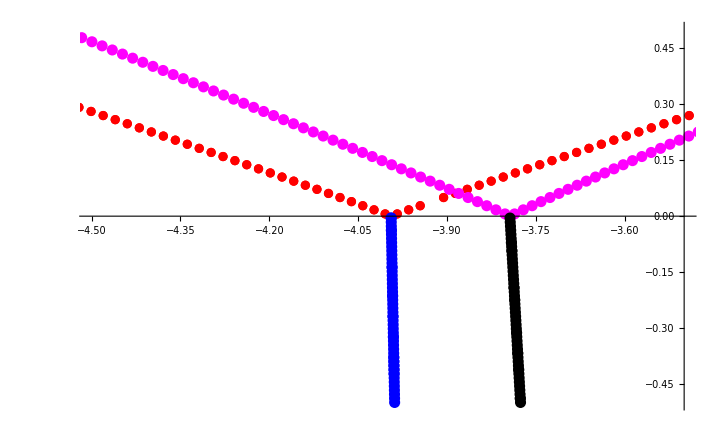

```mathematica
Show[ListPlot[{#[[6]],#[[7]]}&/@crossings1,PlotRange->{{-4.5,-3.5},{-.5,.5}},PlotStyle->Red],ListPlot[{#[[6]],#[[7]]}&/@crossings2,PlotRange->{{-4.5,-3.5},{-.5,.5}},PlotStyle->Magenta],ListPlot[{#[[4]],#[[5]]}&/@cusps2,PlotRange->{{-4.5,-3.5},{-.5,.5}},PlotStyle->Blue],ListPlot[{#[[4]],#[[5]]}&/@cusps1,PlotRange->{{-4.5,-3.5},{-.5,.5}},PlotStyle->Black]]
```

## Phase diagram - 3 hysterons

```mathematica
Clear[var];{a1,b1,c1,d1,a2,c2,k12,k13,a3,b3,c3,d2,k23}={4,1.2,var,-1,4.3,-4,var2,0,4.15,1.1,-4.2,-1,-0.1};
equations={-g+var x1+1.2 x1^2+4 x1^3-var2 (-x1+x2)-k13 (-x1+x3),-g-var2 (x1-x2)-4 x2+x2^2+4.3 x2^3-k23 (-x2+x3),-g-k13 (x1-x3)-k23 (x2-x3)+c3 x3+1.2 x3^2+a3 x3^3};
jacobian=D[equations,{{x1,x2,x3}}];
nullvector=(NullSpace[{{A11,A12,A13},{A12,A22,A23},{A13,A23,A33}}/.{A33->(-A13^2 A22+2 A12 A13 A23-A11 A23^2)/(A12^2-A11 A22)}])/.{A11->D[equations[[1]],x1],A12->D[equations[[1]],x2],A13->D[equations[[1]],x3],A22->D[equations[[2]],x2],A23->D[equations[[2]],x3]};
```

```mathematica
cusppoints[vrb_]:={x1,x2,x3,g,var,vrb}/.NSolve[{(equations/.var2->vrb)==0&&(Det@jacobian/.var2->vrb)==0&&((nullvector.{D[D[equations[[1]],x1],x1]*nullvector[[1,1]]^2,D[D[equations[[2]],x2],x2]*nullvector[[1,2]]^2,D[D[equations[[3]],x3],x3]*nullvector[[1,3]]^2})/.var2->vrb)==0&&Abs[x1]<3&&Abs[x2]<3&&-4.5<=var<=-3.5},{x1,x2,x3,g,var},Reals]
```

```mathematica
cusptable=Table[cusppoints[xx],{xx,-.5,.5,.021}];
```

```mathematica
cusps=Flatten[cusptable,1];
eigenlist1={#[[1]],#[[2]]}&/@Table[Eigenvalues[(jacobian/.{x1->#[[1]],x2->#[[2]],x3->#[[3]],g->#[[4]],var->#[[5]],var2->#[[6]]}&/@cusps)[[n]]],{n,1,Length@cusps}];
condition1=((#[[1]]>0&&#[[2]]>0)&);
selectedindices1=Quiet@Flatten@Position[eigenlist1,_?(condition1)];
```

```mathematica
selectedcusps=cusps[[selectedindices1]];
cusps1={#[[-2]],#[[-1]]}&/@Select[selectedcusps,#[[1]]<0&&#[[2]]<0&&#[[3]]<0&];
cusps2={#[[-2]],#[[-1]]}&/@Select[selectedcusps,#[[1]]>0&&#[[2]]>0&&#[[3]]>0&];
cusps3={#[[-2]],#[[-1]]}&/@Select[selectedcusps,#[[1]]<0&&#[[2]]<0&&#[[3]]>0&];
cusps4={#[[-2]],#[[-1]]}&/@Select[selectedcusps,#[[1]]<0&&#[[2]]>0&&#[[3]]<0&];
cusps5={#[[-2]],#[[-1]]}&/@Select[selectedcusps,#[[1]]>0&&#[[2]]<0&&#[[3]]<0&];
cusps6={#[[-2]],#[[-1]]}&/@Select[selectedcusps,#[[1]]>0&&#[[2]]>0&&#[[3]]<0&];
cusps7={#[[-2]],#[[-1]]}&/@Select[selectedcusps,#[[1]]<0&&#[[2]]>0&&#[[3]]>0&];
cusps8={#[[-2]],#[[-1]]}&/@Select[selectedcusps,#[[1]]>0&&#[[2]]<0&&#[[3]]>0&];
```

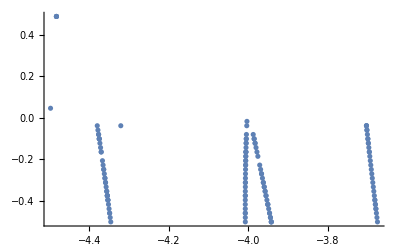

```mathematica
ListPlot[{#[[-2]],#[[-1]]}&/@selectedcusps]
```

```mathematica
crossingpoints[vrb_]:={x1,x2,x3,x4,x5,x6,g,var,vrb}/.NSolve[{(equations/.var2->vrb)==0&&(Det@jacobian/.var2->vrb)==0&&(equations/.{x1->x4,x2->x5,x3->x6,var2->vrb})==0&&(Det@jacobian/.{x1->x4,x2->x5,x3->x6,var2->vrb})==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3&&Abs[x5]<3&&Abs[x6]<3&&Abs[g]<4&&-4.5<=var<-3.5},{x1,x2,x3,x4,x5,x6,g,var},Reals]
```

```mathematica
crossingtable=Table[crossingpoints[xx],{xx,-.5,.5,0.0175}];
```

```mathematica
crossings=Flatten[crossingtable,1];
```

```mathematica
eigenlist2={#[[1]],#[[2]]}&/@Table[Eigenvalues[(jacobian/.{x1->#[[1]],x2->#[[2]],x3->#[[3]],g->#[[7]],var->#[[8]],var2->#[[9]]}&/@crossings)[[n]]],{n,1,Length@crossings}];
eigenlist3={#[[1]],#[[2]]}&/@Table[Eigenvalues[(jacobian/.{x1->#[[4]],x2->#[[5]],x3->#[[6]],g->#[[7]],var->#[[8]],var2->#[[9]]}&/@crossings)[[n]]],{n,1,Length@crossings}];
```

```mathematica
crossingeigenlist=Table[Flatten[Thread[{eigenlist2,eigenlist3}][[n]]],{n,1,Length@eigenlist2}];
condition2=((#[[1]]>0&&#[[2]]>0&&#[[3]]>0&&#[[4]]>0)&);
selectedindices2=Quiet@Flatten@Position[crossingeigenlist,_?(condition2)];
selectedcrossings=Select[crossings[[selectedindices2]],Sign[#[[1]]]==Sign[#[[2]]]||Sign[#[[3]]]==Sign[#[[4]]]>0&];
```

```mathematica
list={selectedcusps,selectedcrossings};
```

```mathematica
Export["cuspcrossinglist.mx",list]
```

cuspcrossinglist.mx

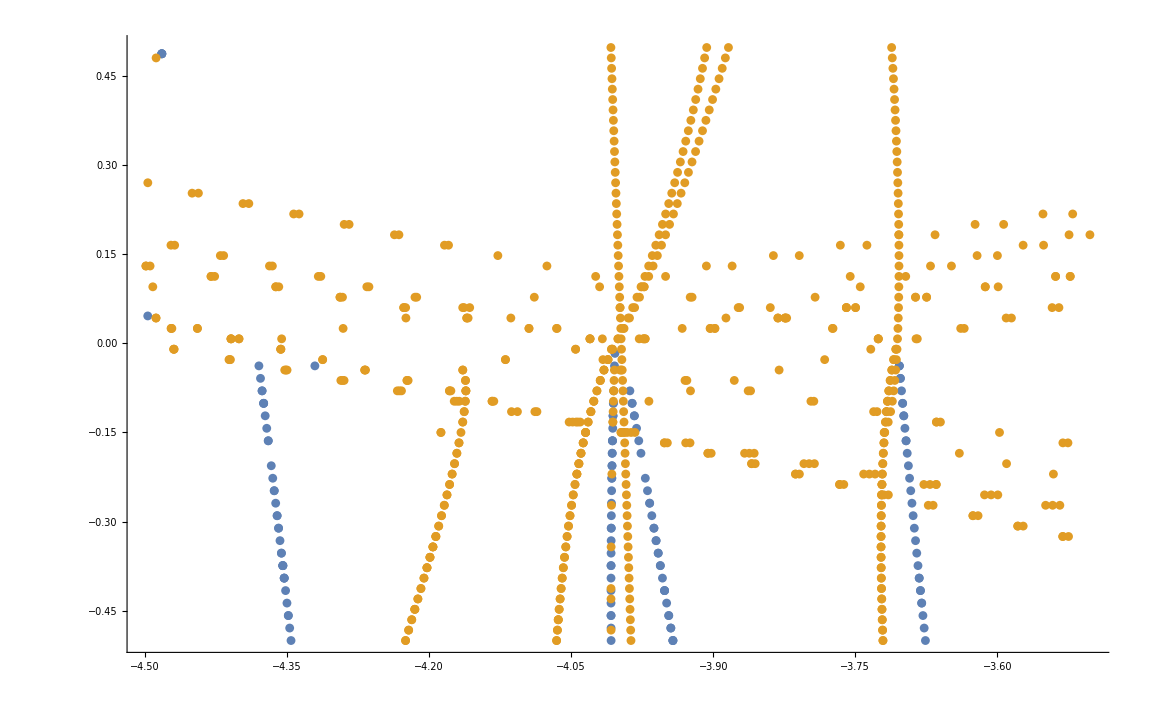

```mathematica
ListPlot[{{#[[-2]],#[[-1]]}&/@selectedcusps,{#[[-2]],#[[-1]]}&/@selectedcrossings}]
```